# Examples of use for the Weaver package

In the following, we demonstrate usage of the Weaver package using a few examples: the Virasoro algebra and the SW(3/2,2) algebra.

To begin, verify that the file Weaver.m is in Mathematica’s path or append Weaver’s path to the $Path variable.

## Virasoro Algebra

Import the package.  This needs to be done with every change of algebra or module: reimporting the package clears saved intermediate results.

```mathematica
<<Weaver.m
```

Weaver: a package for explicit exact-arithmetic calculations in W-algebras

Start by defining the algebra.  Recall that the Virasoro algebra is generated by the operator L_nfor integer n.  New fields can be introduced through the command, AddOperator[operator_name, fermionness, grading, conformal_weight].  The parameters are 

operator_name: the symbol indicating the field.
fermionness:	True if the operator is a fermion and False otherwise
grading:	is n such that the operator takes components in n+Z
conformal weight: the conformal weight of the field.

```mathematica
AddOperator[L,False,0,2];
```

The commutation relations need to be defined explicitly.  The information is given by defining Commutator on the symbols of the operators involved.  Generating sets need to be provided for the various operators.

```mathematica
Commutator[L,n_,L,m_,level_]:=(n-m)Operator[L,n+m,level]+c/12(n^3-n)δ[m+n,level]
MinimalGeneratorsCreation={{L,-1},{L,-2}};
MinimalGeneratorsAnnihilation={{L,1},{L,2}};
```

The modules of the Virasoro algebra are generated by a highest weight subspace of dimension 1:

```mathematica
HighestWeightDimension=1;
```

This is sufficient to define the algebra.  There are a few basic operations that can be explored.  States in the Verma module are written as vectors, each of which corresponds to a series of operators acting on the highest weight space.  Consider the basis states at level 3:

```mathematica
StateNames[3]
```

{{{{L,-3}},1},{{{L,-2},{L,-1}},1},{{{L,-1},{L,-1},{L,-1}},1}}

Each state is described as a pair {operators, i}, which gives the operators acting on the ith highest weight state.  For example, the state {{{L,-2},{L,-1}},1} is L-2L-1|1>.  In order to find the vector associated to this state, you can call

```mathematica
StateVector[{{{L,-2},{L,-1}},1}]
```

{0,1,0}

The action of a given operator on the states at this level is given by the Operator[L,n,level] command, which gives the action of the operator Ln acting on the states at level n.  For example, the action of the operator L1 on the states at level 3 is:

```mathematica
Operator[L,1,3]//MatrixForm
```

(4 | 2 L[0] | 0
0 | 3 | 2 L[0]+2 (1+L[0])+2 (2+L[0]))

Here, L[0] is the L0 eigenvalue of the highest weight state.  There are some useful calculations that can be performed easily once the operators are evaluated.  The Gram matrix and the Kac Determinant at level 4 are given by

```mathematica
GramMatrix[4]//MatrixForm
Factor@Det@%
```

(5 c+8 L[0] | 14 L[0] | 3 c+24 L[0] | 36 L[0] | 120 L[0]
14 L[0] | 12 L[0]+4 c L[0]+12 L[0]^2 | 30 L[0] | 20 L[0]+40 L[0]^2 | 48 L[0]+192 L[0]^2
3 c+24 L[0] | 30 L[0] | 4 c+c^2/2+32 L[0]+8 c L[0]+32 L[0]^2 | 48 L[0]+6 c L[0]+48 L[0]^2 | 144 L[0]+216 L[0]^2
36 L[0] | 20 L[0]+40 L[0]^2 | 48 L[0]+6 c L[0]+48 L[0]^2 | 32 L[0]+2 c L[0]+116 L[0]^2+4 c L[0]^2+32 L[0]^3 | 96 L[0]+336 L[0]^2+288 L[0]^3
120 L[0] | 48 L[0]+192 L[0]^2 | 144 L[0]+216 L[0]^2 | 96 L[0]+336 L[0]^2+288 L[0]^3 | 288 L[0]+1056 L[0]^2+1152 L[0]^3+384 L[0]^4)

384 L[0]^3 (-1+c+8 L[0]) (2+c-7 L[0]+c L[0]+3 L[0]^2) (c-10 L[0]+2 c L[0]+16 L[0]^2)^2 (66+15 c-82 L[0]+10 c L[0]+16 L[0]^2)

Certain other operations are performed more easily without manipulation of symbolic variables.  Specialize now to the Ising model.  The Ising model is a minimal module of the Virasoro algebra, and is isomorphic to the corresponding Verma module quotiented by the nullspace of the Gram matrix.  The character of the minimal model is given by

```mathematica
c=1/2; L[0]=0;

q^(-c/24) (Sum[q^n MatrixRank@GramMatrix@n,{n,0,9}]+O[q]^10)
```

1/q^(1/48)+q^(95/48)+q^(143/48)+2 q^(191/48)+2 q^(239/48)+3 q^(287/48)+3 q^(335/48)+5 q^(383/48)+5 q^(431/48)+O[q]^(479/48)

The singular vectors and the ladder diagram can be calculated directly using the ConstructLadderDiagram[ops,max_level].  ops is a list of the operators by which to label the singular vectors, and max_level is the maximum level to which the algorithm will search.

Singular vectors have dimension 1.

Found singular vector at level 0, with eigenvalues {0}.

Searching for singular vectors at level 1

Singular vectors have dimension 1.

Found singular vector at level 1, with eigenvalues {1}.

Searching for singular vectors at level 2

Searching for singular vectors at level 3

Searching for singular vectors at level 4

Searching for singular vectors at level 5

Searching for singular vectors at level 6

Singular vectors have dimension 1.

Found singular vector at level 6, with eigenvalues {6}.

Searching for singular vectors at level 7

Searching for singular vectors at level 8

Searching for singular vectors at level 9

Searching for singular vectors at level 10

Searching for singular vectors at level 11

Singular vectors have dimension 1.

Found singular vector at level 11, with eigenvalues {11}.

Searching for singular vectors at level 12

Searching for singular vectors at level 13

Singular vectors have dimension 1.

Found singular vector at level 13, with eigenvalues {13}.

Checking parentage of {0} to {1}

Checking parentage of {1} to {6}

Checking parentage of {0} to {6}

Checking parentage of {6} to {11}

Checking parentage of {1} to {11}

Checking parentage of {11} to {13}

Checking parentage of {6} to {13}

Checking parentage of {1} to {13}

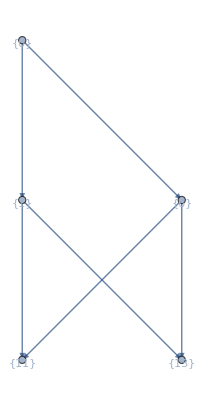

```mathematica
(* This may take a while. *)
{states,parentage}=ConstructLadderDiagram[{L},13];
LadderGraph@@%
```

## SW(3/2,2) algebra

The SW(3/2,2) algebra is defined by Shatashvili and Vafa in arXiv:hep-th/9407025.  This formalism has two bosonic operators, L, and X, and two fermionic operators M, and G.  We will restrict our analysis to the NS sector at c=12.  When writing the commutation relations, we use the command NOperator[G,M,n+m,level] for the normal ordered operator :GM:_(n+m).

```mathematica
<<Weaver.m
AddOperator[L,False,0,2];
AddOperator[X,False,0,2];
AddOperator[G,True,1/2,3/2];
AddOperator[M,True,1/2,5/2];

(* Boson-Boson *)
Commutator[L,n_,L,m_,level_]:=(n-m)Operator[L,n+m,level]+(n^3-n)δ[m+n,level]
Commutator[X,n_,X,m_,level_]:=16/6(n^3-n)δ[m+n,level]+8(n-m)Operator[X,n+m,level]
Commutator[L,n_,X,m_,level_]:= 1/3(n^3-n)δ[m+n,level]+(n-m)Operator[X,n+m,level]
Commutator[X,m_,L,n_,level_]:=-Commutator[L,n,X,m,level]

(* Boson-Fermion and Fermion-Boson *)
Commutator[G,n_,X,m_,level_]:=1/2 (n+1/2) Operator[G,n+m,level]+Operator[M,n+m,level]
Commutator[X,m_,G,n_,level_]:=-Commutator[G,n,X,m,level]
Commutator[X,n_,M,m_,level_]:=(15/4(n+1)(m+3/2)-5/4(n+m+3/2)(n+m+5/2))Operator[G,n+m,level]-(- 8(n+1)+11/2(n+m+5/2))Operator[M,n+m,level]- 6NOperator[G,X,n+m,level]
Commutator[M,m_,X,n_,level_]:=-Commutator[X,n,M,m,level]

Commutator[L,n_,G,m_,level_]:=(1/2 n-m)Operator[G,n+m,level]
Commutator[G,m_,L,n_,level_]:=-Commutator[L,n,G,m,level]
Commutator[L,n_,M,m_,level_]:=1/4 n Operator[G,n+m,level]+1/4 n^2 Operator[G,n+m,level]-m Operator[M,n+m,level]+3/2 n Operator[M,n+m,level]
Commutator[M,m_,L,n_,level_]:=-Commutator[L,n,M,m,level]

(* Fermion-Fermion *)
Commutator[G,n_,M,m_,level_]:=2/3(n^2-1/4)(n-3/2)δ[n+m,level]-(n+1/2)Operator[L,n+m,level]+(3n-m)Operator[X,n+m,level]
Commutator[M,m_,G,n_,level_]:=Commutator[G,n,M,m,level]
Commutator[M,m_,M,n_,level_]:=-8/3(n^2-9/4)(n^2-1/4)δ[n+m,level]+
(15/2(n+3/2)(m+3/2)-5/2(n+m+2)(n+m+3))Operator[L,n+m,level]+
(16(n+3/2)(m+3/2)-5/2(n+m+2)(n+m+3))Operator[X,n+m,level]-  12 NOperator[L,X,n+m,level]+  6 NOperator[G,M,n+m,level]
Commutator[G,m_,G,n_,level_]:=8/2(m^2-1/4)δ[n+m,level]+2Operator[L,n+m,level] 


MinimalGeneratorsCreation={{L,-1},{L,-2},{X,-1},{G,-1/2},{M,-1/2},{M,-5/2}};
MinimalGeneratorsAnnihilation={{L,1},{L,2},{X,1},{X,2},{G,1/2},{M,1/2}};
```

Weaver: a package for explicit exact-arithmetic calculations in operator algebras

The algebra has a nonstandard Hermitian conjugate for the M operators in this formalism.  It is possible to override the default:

```mathematica
HC[M,n_,level_]:= -Operator[M,-n,level-n]-1/2Operator[G,-n,level-n]
```

Restrict to the module generated by L[0]=0, X[0]=0.  This model has singular vectors at level 1/2, 1/2, 2, 4,... and a subsingular vector at level 11/2.  Using this module, the character is

```mathematica
L[0]=0;X[0]=0;
HighestWeightDimension=1;

q^-1(Sum[q^n MatrixRank@GramMatrix@n,{n,0,5,1/2}])+O[q]^(9/2)
```

1/q+√q+2 q+2 q^(3/2)+2 q^2+4 q^(5/2)+7 q^3+8 q^(7/2)+9 q^4+O[q]^(9/2)

Observe that both of the states at level 1/2 are null.  Find Eigenbasis will identify those states by their L[0] and X[0] eigenvalues.  All singular vectors in the module will be descendents of these two states.

```mathematica
states = FindEigenbasis[{L,X},1/2]
```

{{{1/2,5/2},{{1,2}}},{{1/2,1/2},{{1,2/5}}}}

For example, the state {1,2} at level 1/2 is an eigenvector of L[0] and X[0] of values 1/2, and 5/2 respectively.  This is easily checked explicitly.

```mathematica
Print["L_0{1,2}:"];
Operator[L,0,1/2].{1,2}
Print["X_0{1,2}:"];
Operator[X,0,1/2].{1,2}
```

L_0{1,2}:

{1/2,1}

X_0{1,2}:

{5/2,5}

The characters of the submodules of the L,X={1/2,5/2} and {1/2,1/2} are different because there is a level 1/2 creation operator that annihilates the {1/2,1/2} state.  This is easily checked by computing the rank of the descendents.

```mathematica
q^-1(Sum[q^n MatrixRank@Descendents[{1,2},1/2,n],{n,1/2,5,1/2}]+O[q]^(11/2))
q^-1(Sum[q^n MatrixRank@Descendents[{1,2/5},1/2,n],{n,1/2,5,1/2}]+O[q]^(11/2))
```

1/(√q)+2+3 √q+6 q+11 q^(3/2)+18 q^2+28 q^(5/2)+44 q^3+69 q^(7/2)+104 q^4+O[q]^(9/2)

1/(√q)+1+2 √q+4 q+7 q^(3/2)+11 q^2+17 q^(5/2)+27 q^3+42 q^(7/2)+62 q^4+O[q]^(9/2)

The identity of the level 1/2 operator that annihilates L,X={1/2,1/2} can be computed directly.  A basis is given in terms of the operators listed in OperatorNames[level].  The corresponding operator can be evaluated using OperatorNames and OperatorChain.

```mathematica
Print["The vector corresponding to the annihilating operator"];
annopvector=FindAnnihilatingOperators[-1/2 (* level of operator *),{1,2/5},1/2 (* level of state *)]
annop=annopvector[[1]].(OperatorChain[#,1/2]&/@OperatorNames[1/2]);
Print["The action of the annihilating operator on {1,2/5}"];
annop.{1,2/5}
```

The vector corresponding to the annihilating operator

{{-1/2,1}}

The action of the annihilating operator on {1,2/5}

{0,0,0}

A separate function exists for finding null vectors that are not descendents of other null vectors.  Observe that at level 11/2, there is a null element at level 11/2 that is not a descendent of either of the level 1/2 singular vectors.

FindEigenbasis will determine the X eigenspaces at level 11/2.  Observe that the nullspace possesses an additional vector at eigenvalue 65/2 that is not in the space of descendents.

```mathematica
(* This may take a while. *)
Print["Dimensions of the null vectors and the descendents of lower level null vectors."]; 
GramNullspace[11/2]//MatrixRank
NullDescendents[11/2]//MatrixRank

Print["Dimensions of the X eigenspaces at level 11/2:"];
eigenbasis=FindEigenbasis[X,GramNullspace[11/2],11/2];
{#[[1]],MatrixRank[#[[2]]]}&/@eigenbasis

Print["Dimension of the intersection between the eigenspace with eigenvalue 65/2 and the nullspace of the Gram matrix:"]; 
nullintersect = IntersectVectorSpaces[GramNullspace[11/2],eigenbasis[[4,2]]];
MatrixRank[nullintersect]

Print["Dimension of the intersection between the eigenspace with eigenvalue 65/2 and the space of descendents of lower level null vectors:"]; 
descendintersect = IntersectVectorSpaces[NullDescendents[11/2],eigenbasis[[4,2]]];
MatrixRank[descendintersect]

Print["Verify that the third generator of nullintersect is not in descendintersect using InVectorSpaceQ:"];
InVectorSpaceQ[descendintersect,nullintersect[[3]]]

subsingular=nullintersect[[3]];
```

Dimensions of the null vectors and the descendents of lower level null vectors.

208

207

Dimensions of the X eigenspaces at level 11/2:

{{85/2,7},{81/2,7},{69/2,10},{65/2,8},{53/2,15},{49/2,13},{37/2,21},{33/2,18},{21/2,22},{17/2,17},{5/2,36},{1/2,31}}

Dimension of the intersection between the eigenspace with eigenvalue 65/2 and the nullspace of the Gram matrix:

8

Dimension of the intersection between the eigenspace with eigenvalue 65/2 and the space of descendents of lower level null vectors:

7

Verify that the third generator of nullintersect is not in descendintersect using InVectorSpaceQ:

False

Observe the action of negative weight operators on the subsingular vector and verify that they are descendents of singular vectors.  The action of L_1 is shown below.  The other operators act similarly.

```mathematica
Operator[L,1,11/2].subsingular
InVectorSpaceQ[GramNullspace[11/2-1],%]
```

{0,0,0,0,75/32,15/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/32,5/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-25/48,-5/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

True